```mathematica
Avoided Crossing Calculations
```

Avoided Calculations Crossing

1.) Equations of motion of a two coupled oscillator system

```mathematica
m1*x1[t]''+k1*x1[t]+k*(x1[t]-x2[t])==0;
m2*x2[t]''+k2*x2[t]-k*(x1[t]-x2[t])==0;
```

2.) Make ansatz of solution (xi[t]=Ai*Exp[-I*w(+-)*t] and plug into equations above

```mathematica
-m1*w^2*A1+k1*A1+k*(A1+A2)==0;
-m2*w^2*A2*k2*A2-k*(A1-A2)==0;
```

3.) Write equations in matrix form such that when M is multiplied by {A1,A2}, the product is zero

```mathematica
MatrixForm[M={{-m1*w^2+k1+k,-k},{-k,-m2*w^2+k2+k}}]
```

(k+k1-m1 w^2 | -k
-k | k+k2-m2 w^2)

4.) In order for this to be solvable, the determinant of M must be zero

```mathematica
Solve[Det[M]==0,{w}]
```

{{w→-(√(k/m1+k1/m1+k/m2+k2/m2-(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)},{w→(√(k/m1+k1/m1+k/m2+k2/m2-(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)},{w→-(√(k/m1+k1/m1+k/m2+k2/m2+(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)},{w→(√(k/m1+k1/m1+k/m2+k2/m2+(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)}}

5.) Only positive values of w make sense here, so them we get w+ (defined below as wp) and w- (defined below as wm). These are simplified below using the definitions w1 = Sqrt[(k1+k)/m1] and w2 = Sqrt[(k2+k)/m2].

```mathematica
k2=k1+dk;
```

```mathematica
wp[dk_]:=(√(k/m1+k1/m1+k/m2+k2/m2-(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)
```

```mathematica
wm[dk_]:=(√(k/m1+k1/m1+k/m2+k2/m2+(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)
```

6.) Graph solutions to show crossing

```mathematica
k1 =1;
k2=k1+dk;
m1=1;
m2=1;
k=0.1;
```

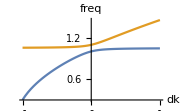

```mathematica
Plot[{wp[dk],wm[dk]},{dk,-1,1}, AxesLabel-> {"dk" ,"freq"}]
```

```mathematica
k1 =1;
k2=k1+dk;
m1=1;
m2=1;
k=0;
```

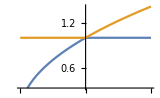

```mathematica
Plot[{wp[dk],wm[dk]},{dk,-1,1}]
```

### Note that sympy agrees with mathematica :

```mathematica
√(k^2 m1^2+2 k k2 m1^2+k2^2 m1^2+2 k^2 m1 m2-2 k k1 m1 m2-2 k k2 m1 m2-2 k1 k2 m1 m2+k^2 m2^2+2 k k1 m2^2+k1^2 m2^2) == √(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2)//FullSimplify
```

True

```mathematica
{-Sqrt[2]*Sqrt[k/m2+k/m1+k1/m1+k2/m2-Sqrt[k^2*m1^2+2*k^2*m1*m2+k^2*m2^2-2*k*k1*m1*m2+2*k*k1*m2^2+2*k*k2*m1^2-2*k*k2*m1*m2+k1^2*m2^2-2*k1*k2*m1*m2+k2^2*m1^2]/(m1*m2)]/2,Sqrt[2]*Sqrt[k/m2+k/m1+k1/m1+k2/m2-Sqrt[k^2*m1^2+2*k^2*m1*m2+k^2*m2^2-2*k*k1*m1*m2+2*k*k1*m2^2+2*k*k2*m1^2-2*k*k2*m1*m2+k1^2*m2^2-2*k1*k2*m1*m2+k2^2*m1^2]/(m1*m2)]/2,-Sqrt[2]*Sqrt[k/m2+k/m1+k1/m1+k2/m2+Sqrt[k^2*m1^2+2*k^2*m1*m2+k^2*m2^2-2*k*k1*m1*m2+2*k*k1*m2^2+2*k*k2*m1^2-2*k*k2*m1*m2+k1^2*m2^2-2*k1*k2*m1*m2+k2^2*m1^2]/(m1*m2)]/2,Sqrt[2]*Sqrt[k/m2+k/m1+k1/m1+k2/m2+Sqrt[k^2*m1^2+2*k^2*m1*m2+k^2*m2^2-2*k*k1*m1*m2+2*k*k1*m2^2+2*k*k2*m1^2-2*k*k2*m1*m2+k1^2*m2^2-2*k1*k2*m1*m2+k2^2*m1^2]/(m1*m2)]/2}
```

{-(√(k/m1+k1/m1+k/m2+k2/m2-(√(k^2 m1^2+2 k k2 m1^2+k2^2 m1^2+2 k^2 m1 m2-2 k k1 m1 m2-2 k k2 m1 m2-2 k1 k2 m1 m2+k^2 m2^2+2 k k1 m2^2+k1^2 m2^2))/(m1 m2)))/(√2),(√(k/m1+k1/m1+k/m2+k2/m2-(√(k^2 m1^2+2 k k2 m1^2+k2^2 m1^2+2 k^2 m1 m2-2 k k1 m1 m2-2 k k2 m1 m2-2 k1 k2 m1 m2+k^2 m2^2+2 k k1 m2^2+k1^2 m2^2))/(m1 m2)))/(√2),-(√(k/m1+k1/m1+k/m2+k2/m2+(√(k^2 m1^2+2 k k2 m1^2+k2^2 m1^2+2 k^2 m1 m2-2 k k1 m1 m2-2 k k2 m1 m2-2 k1 k2 m1 m2+k^2 m2^2+2 k k1 m2^2+k1^2 m2^2))/(m1 m2)))/(√2),(√(k/m1+k1/m1+k/m2+k2/m2+(√(k^2 m1^2+2 k k2 m1^2+k2^2 m1^2+2 k^2 m1 m2-2 k k1 m1 m2-2 k k2 m1 m2-2 k1 k2 m1 m2+k^2 m2^2+2 k k1 m2^2+k1^2 m2^2))/(m1 m2)))/(√2)}

#### Wikipedia' s form that appears to be for 45 degree slope actually isn’t.

```mathematica
Ea = 1/2(E1 + E2) + 1/2 √((E1-E2)^2+4 Abs[W]^2)
Eb =  1/2(E1 + E2) - 1/2 √((E1-E2)^2+4 Abs[W]^2)
```

1/2 (DeltaE+2 E1)+1/2 √(DeltaE^2+4 Abs[W]^2)

1/2 (DeltaE+2 E1)-1/2 √(DeltaE^2+4 Abs[W]^2)

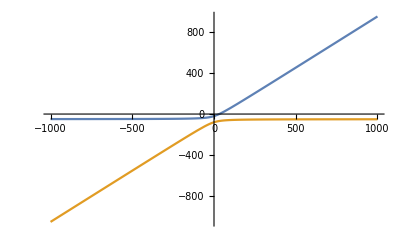

```mathematica
E1 = -50;
W = -30;
Plot[{Ea,Eb}, {DeltaE, -1000,1000}]
```

#### More general form (?) from https://en.wikipedia.org/wiki/Avoided_crossing#General_avoided_crossing_theorem, specifically: https : // wikimedia.org/api/rest_v1/media/math/render/svg/686 e34c4b77a1f5ec894fb07b828e4c7cd6686ef

I found that this did not solve the problem. See below for details.

```mathematica
Clear[Ea, Eb]
```

```mathematica
Ea= 1/2(E1 + E2 + W1 + W2) + 1/2 √((E1-E2+W1-W2)^2+4 W^2);
Eb= 1/2(E1 + E2 + W1 + W2) - 1/2 √((E1-E2+W1-W2)^2+4 W^2);

(* DeltaE = E2 - E1 *)
E2 = DeltaE + E1;
```

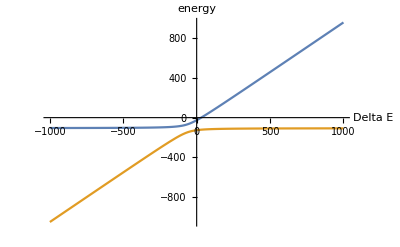

```mathematica
E1 = -56;
W1 = -50;
W2 = 10;
W=40;

Plot[{Ea, Eb}, {DeltaE, -1000, 1000}, AxesLabel-> {"Delta E", "energy"}]

Clear[E1,W1,W2, W]
```

1/2 (DeltaE+2 E1)+1/2 √(DeltaE^2+4 W^2)

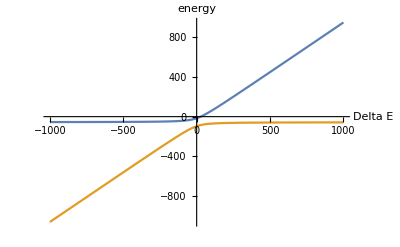

```mathematica
W1 = 0;
W2 = 0;
Ea
E1 = -56;
W=40;

Plot[{Ea, Eb}, {DeltaE, -1000, 1000}, AxesLabel-> {"Delta E", "energy"}]

Clear[E1,W1,W2, W]
```

(* If DeltaE = E1 - E2 is sufficiently large then the W1-W2 will be small in comparison, and we may approximate as follows:  *)

```mathematica
Eaapprox= 1/2(E1 + E2 + W1 + W2) + 1/2 √((E1-E2)^2+4 W^2) // Simplify
Ebapprox= 1/2(E1 + E2 + W1 + W2) - 1/2 √((E1-E2)^2+4 W^2) // Simplify
```

1/2 (DeltaE+2 E1+√(DeltaE^2+4 W^2)+W1+W2)

1/2 (DeltaE+2 E1-√(DeltaE^2+4 W^2)+W1+W2)

```mathematica
D[Eaapprox, DeltaE]
```

1/2 (1+DeltaE/(√(DeltaE^2+4 W^2)))

```mathematica
(* If DeltaE=E1-E2 is sufficiently large then the denominator of the derivative will simplify such that the slope becomes: *)
```

```mathematica
approxslopea = 1/2 (1+DeltaE/DeltaE) // Simplify
```

1

```mathematica
(* The rising slope is at 45 degrees. *)
```

```mathematica
approxslopeaneg = 1/2 (1+DeltaE/-DeltaE) // Simplify
```

0

```mathematica
(* The top line becomes horizontal for negative deltaE*)
```

```mathematica
D[Ebapprox, DeltaE]
```

1/2 (1-DeltaE/(√(DeltaE^2+4 W^2)))

```mathematica
(* If DeltaE=E1-E2 is sufficiently large then the denominator of the derivative will simplify such that the slope becomes: *)
```

```mathematica
approxslopeb = 1/2 (1-DeltaE/DeltaE)
```

0

```mathematica
(* The bottom line becomes horizontal for positive deltaE *)
```

## U shape function from Andrew

```mathematica
σ=.
```

```mathematica
f=√(A-B x^2+CC x^4/σ) (* Eq.4 *)
```

√(A-B x^2+(CC x^4)/σ)

```mathematica
Solve[σ == σ0+DD x^4/σ^2, σ]
```

{{σ→1/3 (σ0+(2^(1/3) σ0^2)/((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))+((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))/2^(1/3))},{σ→σ0/3-((1+ⅈ √3) σ0^2)/(3 2^(2/3) (27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))-((1-ⅈ √3) (27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))/(6 2^(1/3))},{σ→σ0/3-((1-ⅈ √3) σ0^2)/(3 2^(2/3) (27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))-((1+ⅈ √3) (27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))/(6 2^(1/3))}}

```mathematica
σ = 1/3 (σ0+(2^(1/3) σ0^2)/((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))+((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))/2^(1/3));
```

```mathematica
σ /. σ0 -> sigma0 /. DD -> D /. CC -> C// InputForm    (* Format for python. Just need to do ^ -> ** and [ -> ( *)
```

(sigma0 + (2^(1/3)*sigma0^2)/(2*sigma0^3 + 27*D*x^4 + 3*Sqrt[3]*Sqrt[4*D*sigma0^3*x^4 + 27*D^2*x^8])^(1/3) + 
  (2*sigma0^3 + 27*D*x^4 + 3*Sqrt[3]*Sqrt[4*D*sigma0^3*x^4 + 27*D^2*x^8])^(1/3)/2^(1/3))/3

```mathematica
f
```

√(A-B x^2+(3 CC x^4)/(σ0+(2^(1/3) σ0^2)/((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))+((27 DD x^4+2 σ0^3+3 √3 √(27 DD^2 x^8+4 DD x^4 σ0^3))^(1/3))/2^(1/3)))

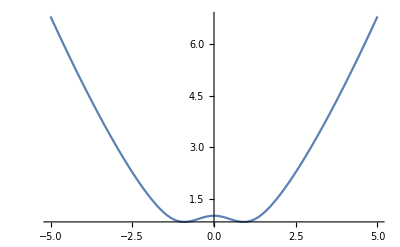

```mathematica
A = 1;
B = 1;
CC = 1;
DD = 1;
σ0=1;

Plot[{f}, {x, -5,5}]
Clear[A,B,CC,DD,σ0]
```

```mathematica
(* From Python: *)
```

```mathematica
sigma = -sigma0^2/(3*(-27*DD*x^4/2-sigma0^3+Sqrt[(-4*sigma0^6+(-27*DD*x^4-2*sigma0^3)^2)]/2)^(1/3))+sigma0/3-(-27*DD*x^4/2-sigma0^3+Sqrt[(-4*sigma0^6+(-27*DD*x^4-2*sigma0^3)^2)]/2)^(1/3)/3
```

sigma0/3-sigma0^2/(3 (-sigma0^3-(27 DD x^4)/2+1/2 √(-4 sigma0^6+(-2 sigma0^3-27 DD x^4)^2))^(1/3))-1/3 (-sigma0^3-(27 DD x^4)/2+1/2 √(-4 sigma0^6+(-2 sigma0^3-27 DD x^4)^2))^(1/3)

```mathematica
σ == sigma  /. sigma0-> σ0// FullSimplify
```

(2 σ0^2)/((-27 DD x^4-2 σ0^3+3 √3 √(DD x^4 (27 DD x^4+4 σ0^3)))^(1/3))+(2 σ0^2)/((27 DD x^4+2 σ0^3+3 √3 √(DD x^4 (27 DD x^4+4 σ0^3)))^(1/3))+(-54 DD x^4-4 σ0^3+6 √3 √(DD x^4 (27 DD x^4+4 σ0^3)))^(1/3)+(54 DD x^4+4 σ0^3+6 √3 √(DD x^4 (27 DD x^4+4 σ0^3)))^(1/3)==0

```mathematica
(* Alas! I do not think the Python and Mathematica solutions are the same! *)
```